## Характеристики графа

Возьмём случайный граф для расчётов

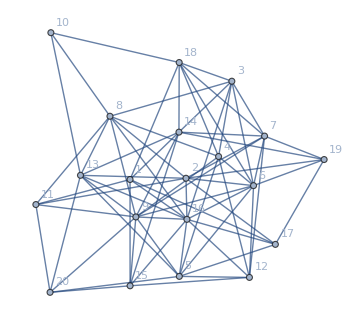

```mathematica
SeedRandom[42];
graph=RandomGraph[BernoulliGraphDistribution[20,0.3],VertexLabels->"Name",ImageSize->Medium]
```

Плотность графа

```mathematica
Clear[graphDensity]
graphDensity::"usage"="Считает плотность графа: отношение количества рёбер к максимально возможному";
graphDensity[graph_Graph?UndirectedGraphQ]:=With[{n=VertexCount@graph,m=EdgeCount@graph},2m/n/(n-1)]
```

```mathematica
GraphDensity@graph
graphDensity@graph
N@%
```

71/190

71/190

0.373684

Матрица расстояний в графе

```mathematica
Clear[findShortestPathes]
findShortestPathes::"usage"="Вычисляет кратчайшие пути (в рёбрах) до всех вершин в графе";
findShortestPathes[edgeList:{__UndirectedEdge},vertex_Integer?Positive]/;MemberQ[VertexList@edgeList,vertex]:=Module[
{distances=ConstantArray[0,VertexCount@edgeList],queue={vertex},scanned={},step=0},
For[
queue={vertex},
queue!={},
queue=Complement[Cases[edgeList,UndirectedEdge[v_,Alternatives@@queue]|UndirectedEdge[Alternatives@@queue,v_]:>v],scanned],
distances⟦queue⟧=step;scanned=Union[scanned,queue];step++
];
distances
]
findShortestPathes[graph_Graph?UndirectedGraphQ]:=findShortestPathes[EdgeList@graph,#]&/@VertexList@graph
```

```mathematica
GraphDistanceMatrix@graph==findShortestPathes@graph
findShortestPathes@graph//MatrixForm
```

True

(0 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 2
2 | 0 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 2
2 | 2 | 0 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 3
2 | 2 | 1 | 0 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 2
2 | 2 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 1
2 | 1 | 1 | 1 | 1 | 0 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2
2 | 1 | 1 | 2 | 2 | 1 | 0 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2
2 | 1 | 1 | 1 | 2 | 2 | 2 | 0 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 0 | 2 | 3 | 1 | 2 | 3 | 2 | 3 | 1 | 3 | 2
1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 3 | 3 | 0 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2
2 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 0 | 1 | 2 | 1 | 2 | 2 | 2 | 1
1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 2 | 2 | 1 | 1 | 2
1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 2 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2 | 1
1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 0 | 1 | 2 | 2 | 2
1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 1 | 0 | 2 | 1 | 2
1 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 0 | 2 | 3
2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 0 | 3
2 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 3 | 3 | 0)

Диаметр графа

```mathematica
Clear[graphDiametr]
graphDiametr::"usage"="Считает диаметр графа (наибольшее из кратчайших расстояний между вершинами в рёбрах)";
graphDiametr[graph_Graph?UndirectedGraphQ]:=Max@findShortestPathes@graph
```

```mathematica
graphDiametr@graph
GraphDiameter@graph
```

3

3

Среднее расстояние в графе

```mathematica
Clear[meanGraphDistance]
meanGraphDistance::"Usage"="Вычисляет среднее расстояние в графе";
meanGraphDistance[graph_Graph?UndirectedGraphQ]:=With[{n=VertexCount@graph},2Total@Flatten@UpperTriangularize@findShortestPathes@graph/n/(n-1)]
```

```mathematica
meanGraphDistance@graph
N@%
```

317/190

1.66842

Коэффициент кластеризации

```mathematica
Clear[forkQ]
forkQ::"usage"="Проверяет, образуют ли дуги вилку";
forkQ[{u_<->v_,x_<->y_}]:=u==x∨u==y∨v==x∨v==y
```

```mathematica
Clear[clusteringCoefficient]
clusteringCoefficient::"usage"="Считает коэффициент кластеризации";
clusteringCoefficient[graph_Graph?UndirectedGraphQ]:=With[{edgeList=EdgeList@graph,vertexList=VertexList@graph},
3Count[UndirectedEdge@@@#&/@(Subsets[#,{2}]&/@Subsets[vertexList,{3}]),_?(SubsetQ[edgeList,#]&)]/Count[Subsets[edgeList,{2}],_?forkQ]]
```

```mathematica
clusteringCoefficient@graph
```

63/158

Локальный кластеризации

```mathematica
Clear[localClusteringCoefficient]
localClusteringCoefficient::"usage"="Считает локальный коэффициент кластеризации";
localClusteringCoefficient[graph_Graph?UndirectedGraphQ,vertex_Integer?Positive]/;MemberQ[VertexList@graph,vertex]:=With[
{edgeList=EdgeList@graph,vertexList=VertexList@graph},
Count[
UndirectedEdge@@@#&/@(Subsets[#,{2}]&/@Sort/@Append[vertex]/@Subsets[DeleteCases[vertexList,vertex,1,1],{2}]),
_?(SubsetQ[edgeList,#]&)
]/Binomial[
Count[edgeList,vertex<->_|_<->vertex],
2
]
]
```

```mathematica
localClusteringCoefficient[graph,#]&/@VertexList@graph
N@%
```

{4/15,5/14,10/21,10/21,13/28,4/9,3/7,11/28,4/11,1/3,3/10,7/15,11/28,9/28,2/5,4/11,2/5,8/21,1/2,1/2}

{0.266667,0.357143,0.47619,0.47619,0.464286,0.444444,0.428571,0.392857,0.363636,0.333333,0.3,0.466667,0.392857,0.321429,0.4,0.363636,0.4,0.380952,0.5,0.5}

Средний коэффициент кластеризации

```mathematica
Clear[meanClusteringCoefficient]
meanClusteringCoefficient::"usage"="Считает локальный коэффициент кластеризации";
meanClusteringCoefficient[graph_Graph?UndirectedGraphQ]:=Mean[localClusteringCoefficient[graph,#]&/@VertexList@graph]
```

```mathematica
meanClusteringCoefficient@graph
N@%
```

1391/3465

0.401443

Степени вершин

```mathematica
Clear[vertexDegree]
vertexDegree::"usage"="Возвращает степени вершин графа";
vertexDegree[graph_Graph?UndirectedGraphQ]:=SortBy[Tally@Flatten[EdgeList@graph,1,UndirectedEdge],First]⟦All,2⟧
```

```mathematica
vertexDegree@graph
VertexDegree@graph
```

{6,8,7,7,8,10,8,8,11,3,5,6,8,8,6,11,5,7,5,5}

{6,8,7,7,8,10,8,8,11,3,5,6,8,8,6,11,5,7,5,5}

Распределение степеней вершин

```mathematica
Clear[vertexDegreeDistribution]
vertexDegreeDistribution::"usage"="Возвращает распределение степеней вершин в формате (d_i, p_i)";
vertexDegreeDistribution[graph_Graph?UndirectedGraphQ]:=Module[
{frequencies=SortBy[Tally@vertexDegree@graph,First]},
frequencies⟦All,2⟧/=Total[frequencies⟦All,2⟧];
frequencies
]
```

```mathematica
vertexDegreeDistribution@graph
MapAt[N,%,{All,2}]
```

{{3,1/20},{5,1/5},{6,3/20},{7,3/20},{8,3/10},{10,1/20},{11,1/10}}

{{3,0.05},{5,0.2},{6,0.15},{7,0.15},{8,0.3},{10,0.05},{11,0.1}}

Степени близости вершин

```mathematica
Clear[graphCloseness]
graphCloseness::"usage"="Величина, обратная среднему расстоянию до других вершин в графе";
graphCloseness[graph_Graph?UndirectedGraphQ]:=With[{n=VertexCount@graph},(n-1)/Total@findShortestPathes[EdgeList@graph,#]&/@VertexList@graph]
```

```mathematica
graphCloseness@graph
N@%
```

{19/32,19/30,19/32,19/31,19/30,19/28,19/30,19/30,19/27,19/39,19/34,19/34,19/30,19/30,19/33,19/27,19/34,19/32,19/35,19/36}

{0.59375,0.633333,0.59375,0.612903,0.633333,0.678571,0.633333,0.633333,0.703704,0.487179,0.558824,0.558824,0.633333,0.633333,0.575758,0.703704,0.558824,0.59375,0.542857,0.527778}

Степень посредничества

```mathematica
Clear[findAllShortestPath]
findAllShortestPath::"usage"="Вспомогательная функция, возвращает список всех кратчайших путей между двумя вершинами в графе";
findAllShortestPath[edgeList_,{s_,t_}]:=FindPath[edgeList,s,t,{Length@FindShortestPath[edgeList,s,t]-1},All]
```

```mathematica
Clear[betweenessCentrality]
betweenessCentrality::"usage"="Возвращает степень посредничества вершины";
betweenessCentrality[graph_Graph?UndirectedGraphQ,vertex_Integer?Positive]/;MemberQ[VertexList@graph,vertex]:=With[
{vertexList=VertexList@graph,edgeList=EdgeList@graph},
Total@Map[
Count[#,_?(MemberQ[#,vertex]&)]/Length@#&,
findAllShortestPath[edgeList,#]&/@Subsets[DeleteCases[vertexList,vertex,1,1],{2}]
]
]
```

```mathematica
betweenessCentrality[graph,#]&/@VertexList@graph
N@%
```

{1643/264,397/45,17/6,6187/1540,21613/2772,6616/693,78469/13860,123/14,4729/330,61/66,5647/1980,139/60,134069/13860,1508/165,1894/495,1063/70,91/36,3743/420,107/60,221/120}

{6.22348,8.82222,2.83333,4.01753,7.7969,9.5469,5.66154,8.78571,14.3303,0.924242,2.85202,2.31667,9.67309,9.13939,3.82626,15.1857,2.52778,8.9119,1.78333,1.84167}

Компоненты связности

```mathematica
Clear[findConnectedComponents]
findConnectedComponents::"usage"="Находит компоненты связности в графе";
findConnectedComponents[edgeList:{__UndirectedEdge},vertex_Integer?Positive]/;MemberQ[VertexList@edgeList,vertex]:=Module[
{queue={},component={}},
For[
queue={vertex},
queue!={},
queue=Complement[Cases[edgeList,UndirectedEdge[v_,Alternatives@@queue]|UndirectedEdge[Alternatives@@queue,v_]:>v],component],
component=Union[component,queue]
];
component
]
findConnectedComponents[graph_Graph?UndirectedGraphQ]:=Reap[NestWhile[
{#⟦1⟧,Complement[#⟦2⟧,Sow@findConnectedComponents[#⟦1⟧,#⟦2,1⟧]]}&,
{EdgeList@graph,VertexList@graph},
#⟦2⟧≠{}&]]⟦2,1⟧
```

```mathematica
Clear[countConnectedComponents]
countConnectedComponents::"usage"="Находит количество компонент связности в графе";
countConnectedComponents[graph_Graph?UndirectedGraphQ]:=Length@findConnectedComponents@graph
```

```mathematica
findConnectedComponents@graph
countConnectedComponents@graph
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}}

1

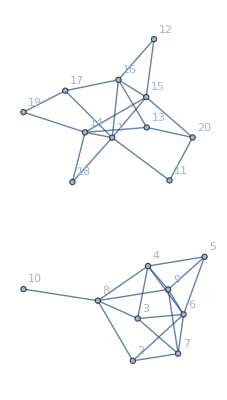

```mathematica
unconnectedGraph=GraphUnion[
Subgraph[graph,Range[2,10]],
Subgraph[graph,Complement[VertexList@graph,Range[2,10]]],
VertexLabels->"Name"
]
```

```mathematica
findConnectedComponents@unconnectedGraph
countConnectedComponents@unconnectedGraph
```

{{1,11,12,13,14,15,16,17,18,19,20},{2,3,4,5,6,7,8,9,10}}

2